```mathematica
rFunc[invS_]:=√((1/invS)/π);
sFunc[r_]:=N[(π r^2)];
invSFunc[r_]:=1./(π r^2);
```

```mathematica
sectionName="NYU-32-X1-87B";

curDir=NotebookDirectory[];
statFile="E:\\05_Segmentation of serial sections\\"<>sectionName<>"_tiles\\results\\_"<>sectionName<>"_total_villous_regions.csv";



data01=Import[statFile,"Table",FieldSeparators->";"];
dataNames=data01[[1]];
data02=data01[[2;;-1]];
```

```mathematica
data01//Dimensions;
data02//Dimensions;
dataNames
```

{Region,Surface(µm.b2),Perimeter(µm),PerimeterContact(µm),PerimeterFrame(µm),NbIVSinsideRegion,SurfaceIVSinsideRegion(µm.b2),PerimeterIVSinsideRegion(µm),NbGR,SurfaceGR(µm.b2),PerimeterGR(µm)}

```mathematica
areaData=data02[[;;,2]];
```

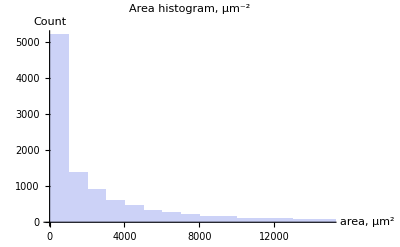

```mathematica
Histogram[areaData,{1000},PlotRange->{{0,15000},All},PlotLabel->"Area histogram, μm^-2",AxesLabel->{"area, μm^2","Count"}]
```

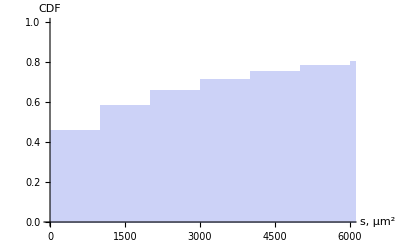

```mathematica
Histogram[areaData,{1000},"CDF",PlotRange->{{0,6000},All},AxesLabel->{"s, μm^2","CDF"}]
```

```mathematica
distribArea=HistogramDistribution[areaData,{100}];
pdfArea=PDF[distribArea,s];
```

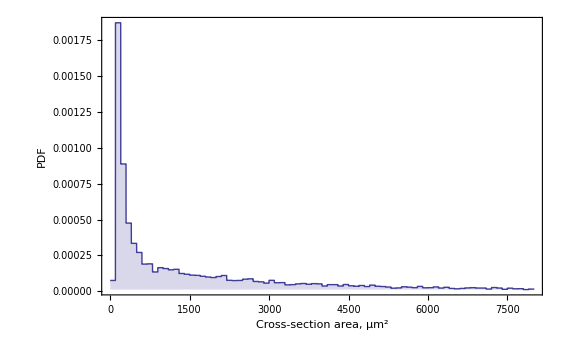

```mathematica
DiscretePlot[pdfArea,{s,0,8000},PlotRange->All,Frame->{{True,False},{True,False}},FrameLabel->{"Cross-section area, μm^2","PDF"},BaseStyle->{FontSize->20}]
```

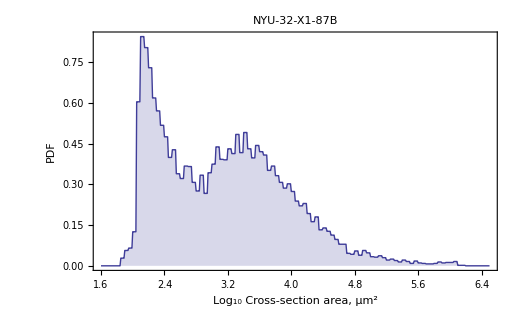

```mathematica
(* A histogram of the distribution of the logarithm of area *)
logAreaData=Log[10,areaData];
distribLogArea=HistogramDistribution[logAreaData,{0.05}];
pdfLogArea=PDF[distribLogArea,s];
DiscretePlot[pdfLogArea,{s,1.6,6.5,0.01},PlotRange->All,Frame->{{True,False},{True,False}},FrameLabel->{"Log_10 Cross-section area, μm^2","PDF"},BaseStyle->{FontSize->20}, PlotLabel->sectionName]
```

```mathematica
distribArea=HistogramDistribution[areaData,{10}];
pdfArea=PDF[distribArea,s];
```

$Aborted

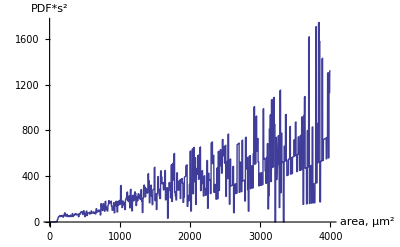

```mathematica
Plot[pdfArea*s^2,{s,0,4000},PlotRange->All,AxesLabel->{"area, μm^2","PDF*s^2"}]
```

```mathematica
boxSize=10;
pdfAreaTempList=HistogramList[areaData,{boxSize},"PDF"];
binsCenters=Table[(pdfAreaTempList[[1,i]]+pdfAreaTempList[[1,i+1]])/2,{i,1,Length[pdfAreaTempList[[1]]]-1}];
pdfAreaList={binsCenters,pdfAreaTempList[[2]]};
pdfAreaList//Dimensions
```

{2,152048}

```mathematica
listPdfArea=Transpose[pdfAreaList];
listPdfAreaCut=Select[listPdfArea,#[[1]]≥150&&#[[1]]≥3000&];(*Select[Transpose[pdfAreaList],#[[2]]>0&]/.{a_,b_}:>{a,b};*)
```

```mathematica
ListPlot[{listPdfArea,listPdfAreaCut},PlotRange->{{0,10000},{0,0.001}},AxesLabel->{"Villous region area, μm^2","PDF"}]
```

-Graphics-

```mathematica
ListLogLogPlot[{listPdfArea,listPdfAreaCut},PlotRange->{{100,10000},{10^-6,0.01}},AxesLabel->{"s, μm^2","PDF"}];
```

```mathematica
(* Fitting with a cylinder sected with a plane *)
fitFunc=a/(π s √(s^2/s0^2-1));
fitParams={a,{s0,110}};
fitResults=FindFit[listPdfAreaCut,{fitFunc,s0>0},fitParams,s]
```

{a→18.883,s0→113.3}

```mathematica
Show[
ListPlot[{listPdfArea,listPdfAreaCut},PlotRange->{{0,10000},{0,0.001}},AxesLabel->{"Villous region area, μm^2","PDF"}],
Plot[fitFunc/.fitResults,{s,100,10^4},PlotRange->{{0,10000},{0,0.001}}]
]
```

-Graphics-

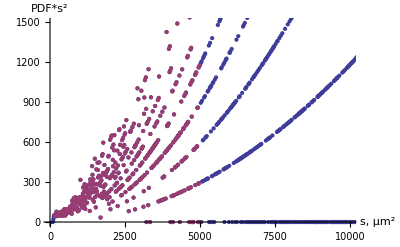

```mathematica
listPdfAreaMultipliedSquare=Transpose[pdfAreaList]/.{a_,b_}:>{a,b*a^2};
listPdfAreaMultipliedSquareCut=Select[listPdfAreaMultipliedSquare,#[[1]]<5000&&#[[1]]>150&];
ListPlot[{listPdfAreaMultipliedSquare,listPdfAreaMultipliedSquareCut},PlotRange->{{0,10000},{0,1500}},AxesOrigin->{Automatic,0},AxesLabel->{"s, μm^2","PDF*s^2"}]
```

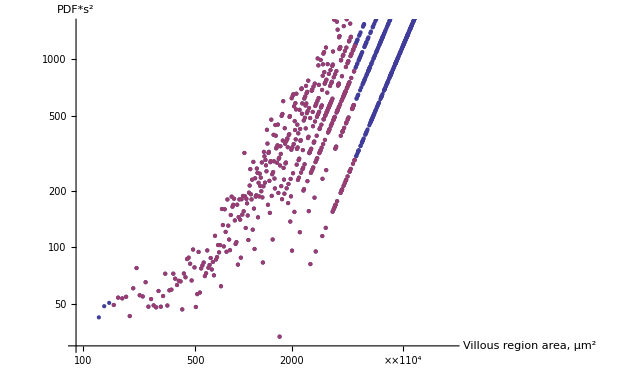

```mathematica
ListLogLogPlot[{listPdfAreaMultipliedSquare,listPdfAreaMultipliedSquareCut},PlotRange->{{90,20000},{30,1500}},AxesOrigin->{Automatic,Automatic},AxesLabel->{"Villous region area, μm^2","PDF*s^2"}]
```

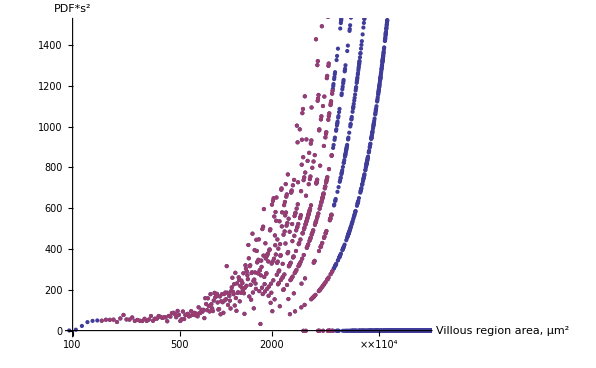

```mathematica
ListLogLinearPlot[{listPdfAreaMultipliedSquare,listPdfAreaMultipliedSquareCut},PlotRange->{{100,2 10^4},{1,1500}}(*{{90,20000},{0,2500}}*),AxesOrigin->{Automatic,Automatic},AxesLabel->{"Villous region area, μm^2","PDF*s^2"}]
```

```mathematica
listPdfAreaMultipliedSquareInversed=listPdfAreaMultipliedSquare/.{a_,b_}:>{a,a^2/b}/;b≠0;
```

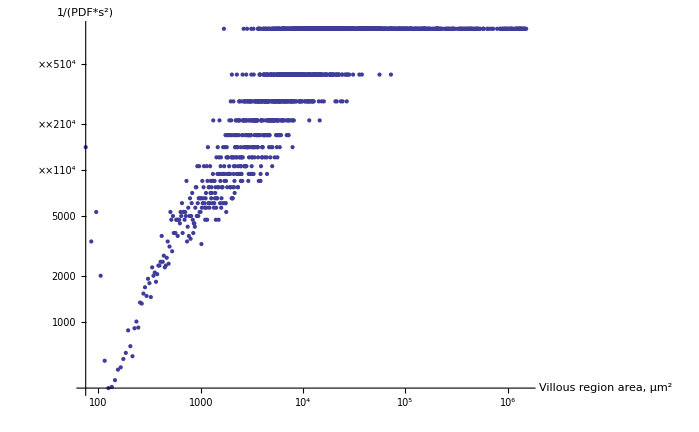

```mathematica
ListLogLogPlot[listPdfAreaMultipliedSquareInversed,PlotRange->All(*,PlotRange->{{90,20000},{30,2500}}*),AxesOrigin->{Automatic,Automatic},AxesLabel->{"Villous region area, μm^2","1/(PDF*s^2)"}]
```

```mathematica
(* Fitting *)
fitFunc=a+b (x-x0)^2/((x-x0)^2+c);
fitParams={{a,40},{b,1000},{c,4 10^6},{x0,150}};
fitResults=FindFit[listPdfAreaMultipliedSquareCut,{fitFunc,a>0,x0>0},fitParams,x]
```

{a→62.1985,b→907.91,c→8.43264×10^6,x0→2.62713×10^-9}

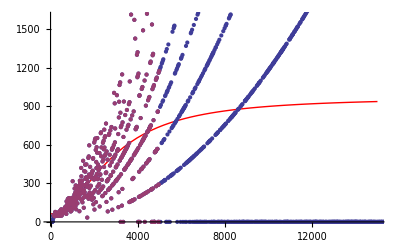

```mathematica
xPlotRange={0,15000};
Show[
Plot[fitFunc/.fitResults,{x,0,15000},PlotStyle->Red],
ListPlot[{listPdfAreaMultipliedSquare,listPdfAreaMultipliedSquareCut},AxesOrigin->{0,0}],PlotRange->{{0,15000},{0,1600}}]
```

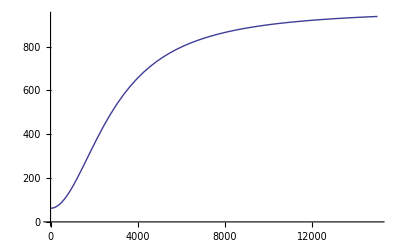

```mathematica
Plot[fitFunc/.fitResults,{x,0,15000},AxesOrigin->{0,0}]
```

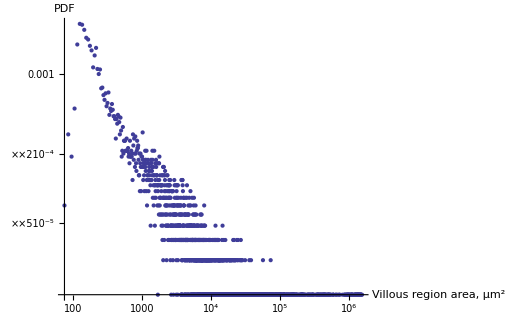

```mathematica
ListLogLogPlot[Transpose[pdfAreaList],PlotRange->All,AxesLabel->{"Villous region area, μm^2","PDF"}]
```

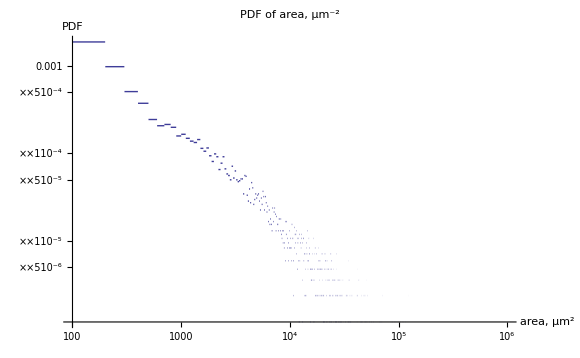

```mathematica
distribArea=HistogramDistribution[areaData,{100}];
pdfArea=PDF[distribArea,s];
LogLogPlot[pdfArea,{s,100,10^6},PlotRange->All,PlotLabel->"PDF of area, μm^-2",AxesLabel->{"area, μm^2","PDF"}]
```

```mathematica
rFunc[{0.004}]
invSFunc[{10,50}]
sFunc[{10,60}]
```

{8.92062}

{0.0031831,0.000127324}

{314.159,11309.7}

```mathematica
inverseAreaData=1/areaData;
```

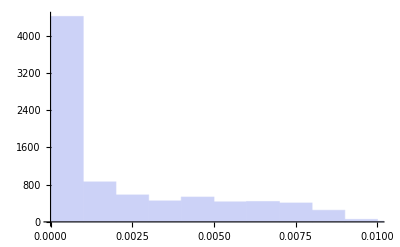

```mathematica
Histogram[inverseAreaData,{0.001},PlotRange->{{0,0.01},All}]
```

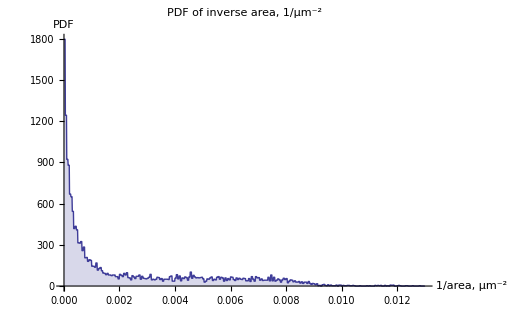

```mathematica
distribInverseArea=HistogramDistribution[inverseAreaData,{0.00005}];
pdfInverseArea=PDF[distribInverseArea,x];
DiscretePlot[pdfInverseArea,{x,0,0.013,0.00001},PlotRange->{{0,0.013},All},PlotLabel->"PDF of inverse area, 1/μm^-2",AxesLabel->{"1/area, μm^-2","PDF"}]
```

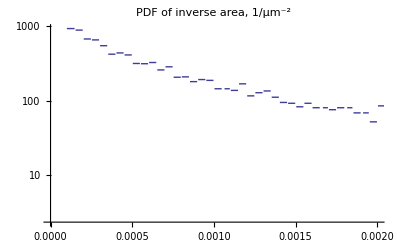

```mathematica
LogPlot[pdfInverseArea,{x,10^-4,0.01},PlotRange->{{0,0.002},All},PlotLabel->"PDF of inverse area, 1/μm^-2"]
```

```mathematica
rFunc[invS_]:=√((1/invS)/π);
sFunc[r_]:=N[(π r^2)];
invSFunc[r_]:=1./(π r^2);
rFunc[{0.004}]
invSFunc[{10,50}]
sFunc[{10,50}]
```

{8.92062}

{0.0031831,0.000127324}

{314.159,7853.98}

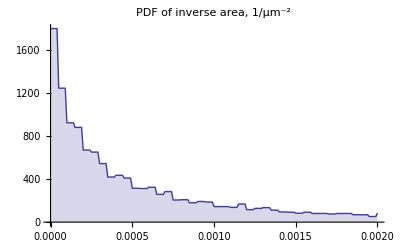

```mathematica
distribInverseArea=HistogramDistribution[inverseAreaData,{0.00005}];
pdfInverseArea=PDF[distribInverseArea,x];
DiscretePlot[pdfInverseArea,{x,0,0.002,0.00001},PlotRange->{{0,0.002},All},AxesOrigin->{0,0},PlotLabel->"PDF of inverse area, 1/μm^-2"]
```